# Bistable motif: detailed balancing and its consequences

Finding the condition of multistationarity

We consider the following reactions:

K+S⇋KS→K+S_p
K^✶+S⇋K^✶S→K^✶+S_p
S_p→S
K⇋K^✶
KS⇋K^✶S

The species of the system are:

{S,S_p,K,K^✶,KS,K^✶S}

In total, there are 11 reations and 6 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms]
```

-k_2^2 k_5^2 k_7 k_8 k_9-2 k_2 k_3 k_5^2 k_7 k_8 k_9-k_3^2 k_5^2 k_7 k_8 k_9-2 k_2^2 k_5 k_6 k_7 k_8 k_9-4 k_2 k_3 k_5 k_6 k_7 k_8 k_9-2 k_3^2 k_5 k_6 k_7 k_8 k_9-k_2^2 k_6^2 k_7 k_8 k_9-2 k_2 k_3 k_6^2 k_7 k_8 k_9-k_3^2 k_6^2 k_7 k_8 k_9-k_2^2 k_5^2 k_7 k_9^2-2 k_2 k_3 k_5^2 k_7 k_9^2-k_3^2 k_5^2 k_7 k_9^2-2 k_2^2 k_5 k_6 k_7 k_9^2-4 k_2 k_3 k_5 k_6 k_7 k_9^2-2 k_3^2 k_5 k_6 k_7 k_9^2-k_2^2 k_6^2 k_7 k_9^2-2 k_2 k_3 k_6^2 k_7 k_9^2-k_3^2 k_6^2 k_7 k_9^2-2 k_2 k_5^2 k_7 k_8 k_9 k_10-2 k_3 k_5^2 k_7 k_8 k_9 k_10-4 k_2 k_5 k_6 k_7 k_8 k_9 k_10-4 k_3 k_5 k_6 k_7 k_8 k_9 k_10-2 k_2 k_6^2 k_7 k_8 k_9 k_10-2 k_3 k_6^2 k_7 k_8 k_9 k_10-2 k_2 k_5^2 k_7 k_9^2 k_10-2 k_3 k_5^2 k_7 k_9^2 k_10-4 k_2 k_5 k_6 k_7 k_9^2 k_10-4 k_3 k_5 k_6 k_7 k_9^2 k_10-2 k_2 k_6^2 k_7 k_9^2 k_10-2 k_3 k_6^2 k_7 k_9^2 k_10-k_5^2 k_7 k_8 k_9 k_10^2-2 k_5 k_6 k_7 k_8 k_9 k_10^2-k_6^2 k_7 k_8 k_9 k_10^2-k_5^2 k_7 k_9^2 k_10^2-2 k_5 k_6 k_7 k_9^2 k_10^2-k_6^2 k_7 k_9^2 k_10^2-2 k_2^2 k_5 k_7 k_8 k_9 k_11-4 k_2 k_3 k_5 k_7 k_8 k_9 k_11-2 k_3^2 k_5 k_7 k_8 k_9 k_11-2 k_2^2 k_6 k_7 k_8 k_9 k_11-4 k_2 k_3 k_6 k_7 k_8 k_9 k_11-2 k_3^2 k_6 k_7 k_8 k_9 k_11-2 k_2^2 k_5 k_7 k_9^2 k_11-4 k_2 k_3 k_5 k_7 k_9^2 k_11-2 k_3^2 k_5 k_7 k_9^2 k_11-2 k_2^2 k_6 k_7 k_9^2 k_11-4 k_2 k_3 k_6 k_7 k_9^2 k_11-2 k_3^2 k_6 k_7 k_9^2 k_11-2 k_2 k_5 k_7 k_8 k_9 k_10 k_11-2 k_3 k_5 k_7 k_8 k_9 k_10 k_11-2 k_2 k_6 k_7 k_8 k_9 k_10 k_11-2 k_3 k_6 k_7 k_8 k_9 k_10 k_11-2 k_2 k_5 k_7 k_9^2 k_10 k_11-2 k_3 k_5 k_7 k_9^2 k_10 k_11-2 k_2 k_6 k_7 k_9^2 k_10 k_11-2 k_3 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_7 k_8 k_9 k_11^2-2 k_2 k_3 k_7 k_8 k_9 k_11^2-k_3^2 k_7 k_8 k_9 k_11^2-k_2^2 k_7 k_9^2 k_11^2-2 k_2 k_3 k_7 k_9^2 k_11^2-k_3^2 k_7 k_9^2 k_11^2+(-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_1^3+(-k_2^2 k_4 k_5 k_6 k_8^2-2 k_2 k_3 k_4 k_5 k_6 k_8^2-k_3^2 k_4 k_5 k_6 k_8^2-k_2^2 k_4 k_6^2 k_8^2-2 k_2 k_3 k_4 k_6^2 k_8^2-k_3^2 k_4 k_6^2 k_8^2-k_2^2 k_4 k_5 k_7 k_8^2-2 k_2 k_3 k_4 k_5 k_7 k_8^2-k_3^2 k_4 k_5 k_7 k_8^2-k_2^2 k_4 k_6 k_7 k_8^2-2 k_2 k_3 k_4 k_6 k_7 k_8^2-k_3^2 k_4 k_6 k_7 k_8^2-k_1 k_2 k_3 k_5^2 k_8 k_9-k_1 k_3^2 k_5^2 k_8 k_9-2 k_1 k_2 k_3 k_5 k_6 k_8 k_9-2 k_1 k_3^2 k_5 k_6 k_8 k_9-k_2^2 k_4 k_5 k_6 k_8 k_9-2 k_2 k_3 k_4 k_5 k_6 k_8 k_9-k_3^2 k_4 k_5 k_6 k_8 k_9-k_1 k_2 k_3 k_6^2 k_8 k_9-k_1 k_3^2 k_6^2 k_8 k_9-k_2^2 k_4 k_6^2 k_8 k_9-2 k_2 k_3 k_4 k_6^2 k_8 k_9-k_3^2 k_4 k_6^2 k_8 k_9-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_8 k_9-k_1 k_3 k_5^2 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-2 k_1 k_2 k_5 k_6 k_7 k_8 k_9-2 k_1 k_3 k_5 k_6 k_7 k_8 k_9-k_1 k_2 k_6^2 k_7 k_8 k_9-k_1 k_3 k_6^2 k_7 k_8 k_9-k_1 k_2 k_3 k_5^2 k_9^2-k_1 k_3^2 k_5^2 k_9^2-2 k_1 k_2 k_3 k_5 k_6 k_9^2-2 k_1 k_3^2 k_5 k_6 k_9^2-k_1 k_2 k_3 k_6^2 k_9^2-k_1 k_3^2 k_6^2 k_9^2-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-2 k_2 k_4 k_5 k_6 k_8^2 k_10-2 k_3 k_4 k_5 k_6 k_8^2 k_10-2 k_2 k_4 k_6^2 k_8^2 k_10-2 k_3 k_4 k_6^2 k_8^2 k_10-2 k_2 k_4 k_5 k_7 k_8^2 k_10-2 k_3 k_4 k_5 k_7 k_8^2 k_10-2 k_2 k_4 k_6 k_7 k_8^2 k_10-2 k_3 k_4 k_6 k_7 k_8^2 k_10-k_1 k_3 k_5^2 k_8 k_9 k_10-k_1 k_2 k_5 k_6 k_8 k_9 k_10-3 k_1 k_3 k_5 k_6 k_8 k_9 k_10-2 k_2 k_4 k_5 k_6 k_8 k_9 k_10-2 k_3 k_4 k_5 k_6 k_8 k_9 k_10-k_1 k_2 k_6^2 k_8 k_9 k_10-2 k_1 k_3 k_6^2 k_8 k_9 k_10-2 k_2 k_4 k_6^2 k_8 k_9 k_10-2 k_3 k_4 k_6^2 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_8 k_9 k_10-k_1 k_3 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-k_1 k_5^2 k_7 k_8 k_9 k_10-k_1 k_2 k_6 k_7 k_8 k_9 k_10-k_1 k_3 k_6 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-2 k_1 k_5 k_6 k_7 k_8 k_9 k_10-k_1 k_6^2 k_7 k_8 k_9 k_10-k_1 k_3 k_5^2 k_9^2 k_10-k_1 k_2 k_5 k_6 k_9^2 k_10-3 k_1 k_3 k_5 k_6 k_9^2 k_10-k_1 k_2 k_6^2 k_9^2 k_10-2 k_1 k_3 k_6^2 k_9^2 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_4 k_5 k_6 k_8^2 k_10^2-k_4 k_6^2 k_8^2 k_10^2-k_4 k_5 k_7 k_8^2 k_10^2-k_4 k_6 k_7 k_8^2 k_10^2-k_1 k_5 k_6 k_8 k_9 k_10^2-k_4 k_5 k_6 k_8 k_9 k_10^2-k_1 k_6^2 k_8 k_9 k_10^2-k_4 k_6^2 k_8 k_9 k_10^2-k_1 k_5 k_7 k_8 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_1 k_6 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_6 k_9^2 k_10^2-k_1 k_6^2 k_9^2 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2 k_3 k_4 k_5 k_8^2 k_11-k_3^2 k_4 k_5 k_8^2 k_11-k_2^2 k_4 k_6 k_8^2 k_11-3 k_2 k_3 k_4 k_6 k_8^2 k_11-2 k_3^2 k_4 k_6 k_8^2 k_11-k_2^2 k_4 k_7 k_8^2 k_11-2 k_2 k_3 k_4 k_7 k_8^2 k_11-k_3^2 k_4 k_7 k_8^2 k_11-k_2 k_4 k_5 k_7 k_8^2 k_11-k_3 k_4 k_5 k_7 k_8^2 k_11-k_2 k_4 k_6 k_7 k_8^2 k_11-k_3 k_4 k_6 k_7 k_8^2 k_11-2 k_1 k_2 k_3 k_5 k_8 k_9 k_11-2 k_1 k_3^2 k_5 k_8 k_9 k_11-k_2 k_3 k_4 k_5 k_8 k_9 k_11-k_3^2 k_4 k_5 k_8 k_9 k_11-2 k_1 k_2 k_3 k_6 k_8 k_9 k_11-2 k_1 k_3^2 k_6 k_8 k_9 k_11-k_2^2 k_4 k_6 k_8 k_9 k_11-3 k_2 k_3 k_4 k_6 k_8 k_9 k_11-2 k_3^2 k_4 k_6 k_8 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_8 k_9 k_11-2 k_1 k_3 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-2 k_1 k_2 k_6 k_7 k_8 k_9 k_11-2 k_1 k_3 k_6 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_3 k_5 k_9^2 k_11-2 k_1 k_3^2 k_5 k_9^2 k_11-2 k_1 k_2 k_3 k_6 k_9^2 k_11-2 k_1 k_3^2 k_6 k_9^2 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_3 k_4 k_5 k_8^2 k_10 k_11-k_2 k_4 k_6 k_8^2 k_10 k_11-2 k_3 k_4 k_6 k_8^2 k_10 k_11-k_2 k_4 k_7 k_8^2 k_10 k_11-k_3 k_4 k_7 k_8^2 k_10 k_11-k_4 k_5 k_7 k_8^2 k_10 k_11-k_4 k_6 k_7 k_8^2 k_10 k_11-k_1 k_3 k_5 k_8 k_9 k_10 k_11-k_3 k_4 k_5 k_8 k_9 k_10 k_11-k_1 k_2 k_6 k_8 k_9 k_10 k_11-2 k_1 k_3 k_6 k_8 k_9 k_10 k_11-k_2 k_4 k_6 k_8 k_9 k_10 k_11-2 k_3 k_4 k_6 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_7 k_8 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_1 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_1 k_6 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_5 k_9^2 k_10 k_11-k_1 k_2 k_6 k_9^2 k_10 k_11-2 k_1 k_3 k_6 k_9^2 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2 k_3 k_4 k_8^2 k_11^2-k_3^2 k_4 k_8^2 k_11^2-k_2 k_4 k_7 k_8^2 k_11^2-k_3 k_4 k_7 k_8^2 k_11^2-k_1 k_2 k_3 k_8 k_9 k_11^2-k_1 k_3^2 k_8 k_9 k_11^2-k_2 k_3 k_4 k_8 k_9 k_11^2-k_3^2 k_4 k_8 k_9 k_11^2-k_1 k_2 k_7 k_8 k_9 k_11^2-k_1 k_3 k_7 k_8 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_3 k_9^2 k_11^2-k_1 k_3^2 k_9^2 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2) x_3+x_1^2 (-k_1 k_2 k_4 k_5 k_7 k_9 k_10-k_1 k_3 k_4 k_5 k_7 k_9 k_10-k_1 k_2 k_4 k_6 k_7 k_9 k_10-k_1 k_3 k_4 k_6 k_7 k_9 k_10-k_1 k_4 k_5 k_7 k_9 k_10^2-k_1 k_4 k_6 k_7 k_9 k_10^2-k_2^2 k_4^2 k_7 k_8 k_11-2 k_2 k_3 k_4^2 k_7 k_8 k_11-k_3^2 k_4^2 k_7 k_8 k_11-2 k_1 k_2 k_4 k_5 k_7 k_9 k_11-2 k_1 k_3 k_4 k_5 k_7 k_9 k_11-2 k_1 k_2 k_4 k_6 k_7 k_9 k_11-2 k_1 k_3 k_4 k_6 k_7 k_9 k_11-k_1 k_2 k_4 k_5 k_7 k_10 k_11-k_1 k_3 k_4 k_5 k_7 k_10 k_11-k_1 k_2 k_4 k_6 k_7 k_10 k_11-k_1 k_3 k_4 k_6 k_7 k_10 k_11-k_2 k_4^2 k_7 k_8 k_10 k_11-k_3 k_4^2 k_7 k_8 k_10 k_11-2 k_1 k_2 k_4 k_7 k_9 k_10 k_11-2 k_1 k_3 k_4 k_7 k_9 k_10 k_11-k_1 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_4 k_6 k_7 k_9 k_10 k_11-k_2^2 k_4^2 k_7 k_11^2-2 k_2 k_3 k_4^2 k_7 k_11^2-k_3^2 k_4^2 k_7 k_11^2-k_2 k_4^2 k_7 k_8 k_11^2-k_3 k_4^2 k_7 k_8 k_11^2-2 k_1 k_2 k_4 k_7 k_9 k_11^2-2 k_1 k_3 k_4 k_7 k_9 k_11^2+(k_1^2 k_3 k_4 k_5 k_9 k_10+k_1^2 k_3 k_4 k_6 k_9 k_10-k_1^2 k_4 k_5 k_6 k_9 k_10-k_1^2 k_4 k_6^2 k_9 k_10-k_1^2 k_4 k_5 k_6 k_10^2-k_1^2 k_4 k_6^2 k_10^2-k_1^2 k_4 k_5 k_7 k_10^2-k_1^2 k_4 k_6 k_7 k_10^2-k_1 k_2 k_3 k_4^2 k_8 k_11-k_1 k_3^2 k_4^2 k_8 k_11+k_1 k_2 k_4^2 k_6 k_8 k_11+k_1 k_3 k_4^2 k_6 k_8 k_11-k_1^2 k_3 k_4 k_5 k_10 k_11-k_1^2 k_3 k_4 k_6 k_10 k_11-k_1 k_2 k_4^2 k_6 k_10 k_11-k_1 k_3 k_4^2 k_6 k_10 k_11-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1^2 k_4 k_5 k_7 k_10 k_11-k_1^2 k_4 k_6 k_7 k_10 k_11-k_1 k_2 k_3 k_4^2 k_11^2-k_1 k_3^2 k_4^2 k_11^2-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_3)+x_1 (-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-k_1 k_2 k_5^2 k_7 k_9 k_10-k_1 k_3 k_5^2 k_7 k_9 k_10-2 k_1 k_2 k_5 k_6 k_7 k_9 k_10-2 k_1 k_3 k_5 k_6 k_7 k_9 k_10-k_1 k_2 k_6^2 k_7 k_9 k_10-k_1 k_3 k_6^2 k_7 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9 k_10^2-2 k_1 k_5 k_6 k_7 k_9 k_10^2-k_1 k_6^2 k_7 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2^2 k_4 k_5 k_7 k_8 k_11-2 k_2 k_3 k_4 k_5 k_7 k_8 k_11-k_3^2 k_4 k_5 k_7 k_8 k_11-k_2^2 k_4 k_6 k_7 k_8 k_11-2 k_2 k_3 k_4 k_6 k_7 k_8 k_11-k_3^2 k_4 k_6 k_7 k_8 k_11-2 k_2^2 k_4 k_5 k_7 k_9 k_11-4 k_2 k_3 k_4 k_5 k_7 k_9 k_11-2 k_3^2 k_4 k_5 k_7 k_9 k_11-2 k_2^2 k_4 k_6 k_7 k_9 k_11-4 k_2 k_3 k_4 k_6 k_7 k_9 k_11-2 k_3^2 k_4 k_6 k_7 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_2 k_4 k_5 k_7 k_8 k_10 k_11-k_3 k_4 k_5 k_7 k_8 k_10 k_11-k_2 k_4 k_6 k_7 k_8 k_10 k_11-k_3 k_4 k_6 k_7 k_8 k_10 k_11-k_1 k_2 k_5 k_7 k_9 k_10 k_11-k_1 k_3 k_5 k_7 k_9 k_10 k_11-2 k_2 k_4 k_5 k_7 k_9 k_10 k_11-2 k_3 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_2 k_6 k_7 k_9 k_10 k_11-k_1 k_3 k_6 k_7 k_9 k_10 k_11-2 k_2 k_4 k_6 k_7 k_9 k_10 k_11-2 k_3 k_4 k_6 k_7 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_4 k_7 k_8 k_11^2-2 k_2 k_3 k_4 k_7 k_8 k_11^2-k_3^2 k_4 k_7 k_8 k_11^2-2 k_2^2 k_4 k_7 k_9 k_11^2-4 k_2 k_3 k_4 k_7 k_9 k_11^2-2 k_3^2 k_4 k_7 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2-2 (k_1 k_2 k_4 k_5 k_6 k_8 k_10+k_1 k_3 k_4 k_5 k_6 k_8 k_10+k_1 k_2 k_4 k_6^2 k_8 k_10+k_1 k_3 k_4 k_6^2 k_8 k_10+k_1 k_2 k_4 k_5 k_7 k_8 k_10+k_1 k_3 k_4 k_5 k_7 k_8 k_10+k_1 k_2 k_4 k_6 k_7 k_8 k_10+k_1 k_3 k_4 k_6 k_7 k_8 k_10+k_1 k_2 k_4 k_5 k_6 k_9 k_10+k_1 k_3 k_4 k_5 k_6 k_9 k_10+k_1 k_2 k_4 k_6^2 k_9 k_10+k_1 k_3 k_4 k_6^2 k_9 k_10+k_1 k_2 k_4 k_5 k_7 k_9 k_10+k_1 k_3 k_4 k_5 k_7 k_9 k_10+k_1 k_2 k_4 k_6 k_7 k_9 k_10+k_1 k_3 k_4 k_6 k_7 k_9 k_10+k_1 k_4 k_5 k_6 k_8 k_10^2+k_1 k_4 k_6^2 k_8 k_10^2+k_1 k_4 k_5 k_7 k_8 k_10^2+k_1 k_4 k_6 k_7 k_8 k_10^2+k_1 k_4 k_5 k_6 k_9 k_10^2+k_1 k_4 k_6^2 k_9 k_10^2+k_1 k_4 k_5 k_7 k_9 k_10^2+k_1 k_4 k_6 k_7 k_9 k_10^2+k_1 k_2 k_3 k_4 k_5 k_8 k_11+k_1 k_3^2 k_4 k_5 k_8 k_11+k_1 k_2 k_3 k_4 k_6 k_8 k_11+k_1 k_3^2 k_4 k_6 k_8 k_11+k_1 k_2 k_4 k_5 k_7 k_8 k_11+k_1 k_3 k_4 k_5 k_7 k_8 k_11+k_1 k_2 k_4 k_6 k_7 k_8 k_11+k_1 k_3 k_4 k_6 k_7 k_8 k_11+k_1 k_2 k_3 k_4 k_5 k_9 k_11+k_1 k_3^2 k_4 k_5 k_9 k_11+k_1 k_2 k_3 k_4 k_6 k_9 k_11+k_1 k_3^2 k_4 k_6 k_9 k_11+k_1 k_2 k_4 k_5 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_7 k_9 k_11+k_1 k_2 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_8 k_10 k_11+k_1 k_2 k_4 k_6 k_8 k_10 k_11+2 k_1 k_3 k_4 k_6 k_8 k_10 k_11+k_1 k_2 k_4 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_7 k_8 k_10 k_11+k_1 k_4 k_5 k_7 k_8 k_10 k_11+k_1 k_4 k_6 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_5 k_9 k_10 k_11+k_1 k_2 k_4 k_6 k_9 k_10 k_11+2 k_1 k_3 k_4 k_6 k_9 k_10 k_11+k_1 k_2 k_4 k_7 k_9 k_10 k_11+k_1 k_3 k_4 k_7 k_9 k_10 k_11+k_1 k_4 k_5 k_7 k_9 k_10 k_11+k_1 k_4 k_6 k_7 k_9 k_10 k_11+k_1 k_2 k_3 k_4 k_8 k_11^2+k_1 k_3^2 k_4 k_8 k_11^2+k_1 k_2 k_4 k_7 k_8 k_11^2+k_1 k_3 k_4 k_7 k_8 k_11^2+k_1 k_2 k_3 k_4 k_9 k_11^2+k_1 k_3^2 k_4 k_9 k_11^2+k_1 k_2 k_4 k_7 k_9 k_11^2+k_1 k_3 k_4 k_7 k_9 k_11^2) x_3)

```mathematica
factor=Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
Factor[factor]
```

k_1 k_4 (k_1 k_3 k_5 k_9 k_10+k_1 k_3 k_6 k_9 k_10-k_1 k_5 k_6 k_9 k_10-k_1 k_6^2 k_9 k_10-k_1 k_5 k_6 k_10^2-k_1 k_6^2 k_10^2-k_1 k_5 k_7 k_10^2-k_1 k_6 k_7 k_10^2-k_2 k_3 k_4 k_8 k_11-k_3^2 k_4 k_8 k_11+k_2 k_4 k_6 k_8 k_11+k_3 k_4 k_6 k_8 k_11-k_1 k_3 k_5 k_10 k_11-k_1 k_3 k_6 k_10 k_11-k_2 k_4 k_6 k_10 k_11-k_3 k_4 k_6 k_10 k_11-k_2 k_4 k_7 k_10 k_11-k_3 k_4 k_7 k_10 k_11-k_1 k_5 k_7 k_10 k_11-k_1 k_6 k_7 k_10 k_11-k_2 k_3 k_4 k_11^2-k_3^2 k_4 k_11^2-k_2 k_4 k_7 k_11^2-k_3 k_4 k_7 k_11^2)

```mathematica
term=Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
simpTerm=FullSimplify[term]
```

-(k_2+k_3) k_4 k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11))-k_1 (k_5+k_6) k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11))

```mathematica
simplerTerm=Distribute[simpTerm/(Subscript[k, 1]*Subscript[k, 4])]/.{(Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1]-> Subscript[M, 1],(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]-> Subscript[M, 2]}
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2

This above term larger than 0 should be the necessary condition.

```mathematica
condition=simplerTerm>0
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2>0

By mannual simplying the term, we can have:

```mathematica
simpleCond=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])>(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))
```

(k_3-k_6) (-k_8 k_11 M_1+k_9 k_10 M_2)>(k_6 k_10+k_3 k_11+k_7 (k_10+k_11)) (k_11 M_1+k_10 M_2)

```mathematica
left=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)

```mathematica
right=(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

To fullfile the assumption of thermodynamic conditions for the reversible reactions, we have the the constraint:
(k_1 k_10)/(k_2 k_11)=(k_4 k_8)/(k_5 k_9).
This will give us a even simple condition. Then we will example how will this condition result in the parameter space for multistationarity.

```mathematica
oriCond=simpleCond/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

```mathematica
Simplify[oriCond,Assumptions->(Subscript[k, 1] Subscript[k, 10])/(Subscript[k, 2] Subscript[k, 11])==(Subscript[k, 4] Subscript[k, 8])/(Subscript[k, 5] Subscript[k, 9])]
```

((k_3-k_6) (k_1 k_6 k_9 k_10-k_3 k_4 k_8 k_11))/(k_1 k_4)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Better to do it manually, then we have the condition with thermodynamic constraint:

```mathematica
thermoCond=(Subscript[k, 3]-Subscript[k, 6])(Subscript[k, 6] Subscript[k, 2]-Subscript[k, 3] Subscript[k, 5])>(Subscript[k, 2]/Subscript[k, 9]×(Subscript[k, 5]^2 +Subscript[k, 6])/Subscript[k, 5]+Subscript[k, 5]/Subscript[k, 8]×(Subscript[k, 2]^2+Subscript[k, 3])/Subscript[k, 2])((Subscript[k, 6]+Subscript[k, 7]) Subscript[k, 10]+(Subscript[k, 3]+Subscript[k, 7]) Subscript[k, 11])
```

(k_3-k_6) (-k_3 k_5+k_2 k_6)>(((k_2^2+k_3) k_5)/(k_2 k_8)+(k_2 (k_5^2+k_6))/(k_5 k_9)) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Fromt the above condition, we can get some general idea that in order to satisfy the thermodynamic condition we should have:
Necessarily:
k_3>k_6 and k_2>k_5
or
k_3<k_6 and k_5>k_2
With additional:
k_8,k_9≫k_10,k_11 and k_7,k_10,k_11≈0

Sampling the parameters (without thermodynamic constraint)

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)

bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
rands=Exp[RandomReal[{0,1},11]*2*Log[1000]-Log[1000]];
k1=rands[[1]];k2=rands[[2]];k3=rands[[3]];k4=rands[[4]];k5=rands[[5]];k6=rands[[6]];k7=rands[[7]];k8=rands[[8]];k9=rands[[9]];k10=rands[[10]];k11=rands[[11]];
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11}];
(*counter=1;hitQ=0;
While[hitQ==0&&counter≤1000,{
x1=RandomReal[{0,1000}];
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[T1≤1000&&T2≤1000,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
counter++;
}];*)
}];
},{i,100000}];
]
```

{4.43198,Null}

```mathematica
Length[bistableKs]
```

14377

```mathematica
tKs=Transpose[bistableKs];
km1=(tKs[[2]]+tKs[[3]])/tKs[[1]];
km2=(tKs[[5]]+tKs[[6]])/tKs[[4]];
kd1=tKs[[9]]/tKs[[8]];
kd2=tKs[[11]]/tKs[[10]];
c1=tKs[[3]]/tKs[[6]];
c2=(km1*kd2)/(km2*kd1);
```

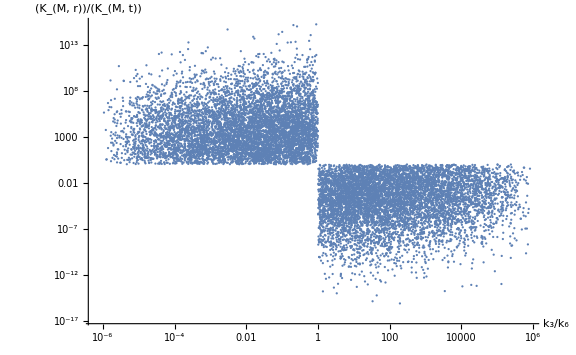

```mathematica
kdPlot=ListLogLogPlot[Transpose[{c1,c2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"k_3/k_6","(K_(M, r))/(K_(M, t))"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Minimal"]
```

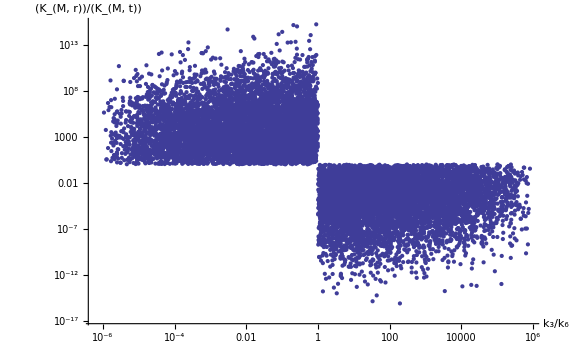

```mathematica
kdPlot=ListLogLogPlot[Transpose[{c1,c2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"k_3/k_6","(K_(M, r))/(K_(M, t))"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Classic"]
```

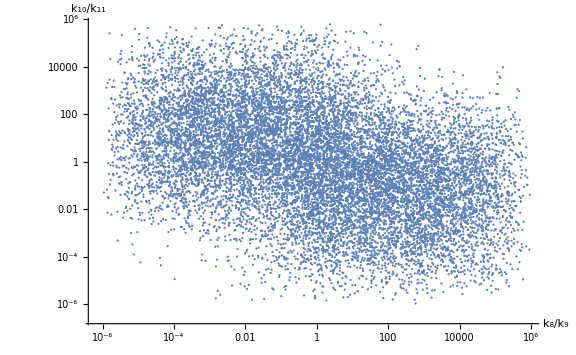

```mathematica
kmPlot=ListLogLogPlot[Transpose[{kd1,kd2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},(*AxesLabel->{"K_M1","K_M2"},*)AxesLabel->{"k_8/k_9","k_10/k_11"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Default"]
```

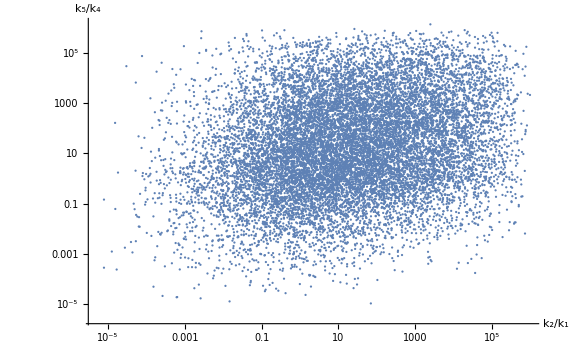

```mathematica
kdPlot=ListLogLogPlot[Transpose[{km1,km2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},(*AxesLabel->{"K_D1","K_D2"},*)AxesLabel->{"k_2/k_1","k_5/k_4"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Default"]
```

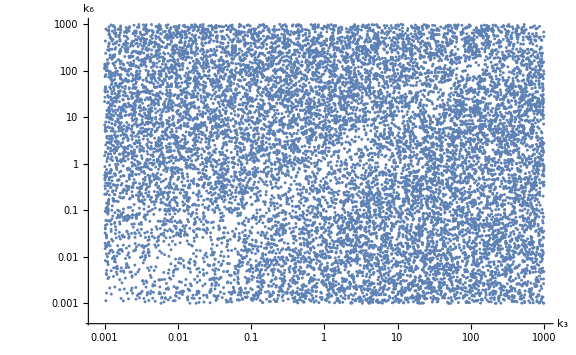

```mathematica
kdPlot=ListLogLogPlot[Transpose[{tKs[[3]],tKs[[6]]}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"k_3","k_6"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Default"]
```

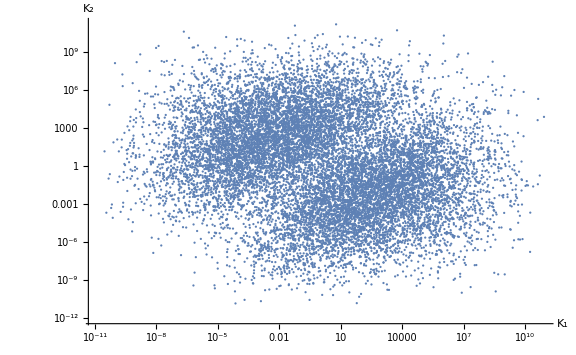

```mathematica
kdPlot=ListLogLogPlot[Transpose[{tKs[[1]]*tKs[[10]]*tKs[[5]]*tKs[[9]],tKs[[2]]*tKs[[11]]*tKs[[4]]*tKs[[8]]}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Default"]
```

```mathematica
model=LinearModelFit[Transpose[{Log10[kd1],Log10[kd2]}],x,x]
```

FittedModel[0.00994391-0.304079 x]

```mathematica
InputForm[model["BestFit"]]
```

0.00994391374582708 - 0.30407856141463835*x

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00994391 | 0.0172304 | 0.577115 | 0.56387
x | -0.304079 | 0.00634757 | -47.9047 | 8.3820228558×10^-465

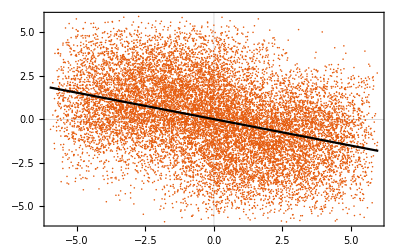

```mathematica
Show[ListPlot[Transpose[{Log10[kd1],Log10[kd2]}],PlotTheme->"Scientific"],Plot[model["BestFit"],{x,-6,6},PlotTheme->"Monochrome"]]
```

```mathematica
ListPointPlot3D[DimensionReduce[Transpose[{km1,km2,kd1,kd2,tKs[[7]]}],3]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[DimensionReduce[bistableKs,3,Method->"PrincipalComponentsAnalysis",PerformanceGoal->"Quality"]]
```

-Graphics3D-

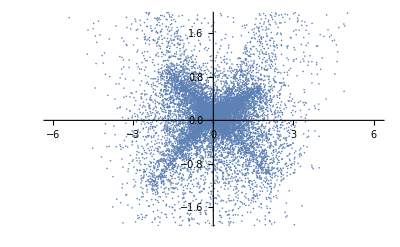

```mathematica
ListPlot[DimensionReduce[bistableKs,2,Method->"PrincipalComponentsAnalysis",PerformanceGoal->"Quality"]]
```

Sampling the parameters (with thermodynamic constraint)

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

Sampling the parameters related to thermodynamic constraint k1, k2, k4, k5, k8, k9, k10, k11. Using Gamma distribution with α = 7, β = 2, and then uniformly sample 4 random numbers that sum to 1, these are for k1, k5, k9, k10. Sample anther four uniform random number for k2, k4, k8, k11.

For other parameters:

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)


bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
others=Exp[RandomReal[{0,1},3]*2*Log[1000]-Log[1000]];
While[(rand1s=RandomReal[{0,1},4];sum=Total@rand1s;psum=Switch[True,0≤#≤1,1./4*sum^3,1<#≤2,1/4*(-3*sum^3+12*sum^2-12*sum+4),2<#≤3,1/4*(3*sum^3-24*sum^2+60*sum-44),3<#≤4,1/4*(-sum^3+12*sum^2-48*sum+64)]&[sum];
RandomReal≤psum)];
rand23=RandomVariate[DirichletDistribution[{1,1,1,1}]];
rand21=1-Total@rand23;
k1=Exp[rand1s[[1]]/sum*2*Log[1000]-Log[1000]];k2=Exp[rand23[[1]]*2*Log[1000]-Log[1000]];k3=others[[1]];k4=Exp[rand23[[2]]*2*Log[1000]-Log[1000]];k5=Exp[rand1s[[2]]/sum*2*Log[1000]-Log[1000]];k6=others[[2]];k7=others[[3]];
k8=Exp[rand23[[3]]*2*Log[1000]-Log[1000]];
k9=Exp[rand1s[[3]]/sum*2*Log[1000]-Log[1000]];
k10=Exp[rand1s[[4]]/sum*2*Log[1000]-Log[1000]];
k11=Exp[rand21*2*Log[1000]-Log[1000]];
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11}];
(*counter=1;hitQ=0;
While[hitQ==0&&counter≤1000,{
x1=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.0001])]]]*1000;
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[0.0001≤T1≤1000&&0.0001≤T2≤1000,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
counter++;
}];*)
}];
},{i,100000}];
]
```

{124.748,Null}

```mathematica
Length[bistableKs]
```

11305

```mathematica
tKs=Transpose[bistableKs];
km1=(tKs[[2]]+tKs[[3]])/tKs[[1]];
km2=(tKs[[5]]+tKs[[6]])/tKs[[4]];
kd1=tKs[[9]]/tKs[[8]];
kd2=tKs[[11]]/tKs[[10]];
c1=tKs[[3]]/tKs[[6]];
c2=(km1*kd2)/(km2*kd1);
```

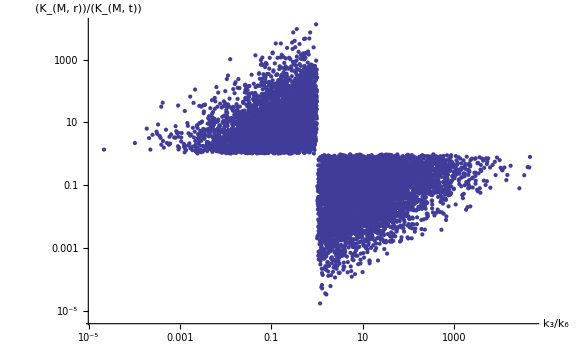

```mathematica
kdPlot=ListLogLogPlot[Transpose[{c1,c2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"k_3/k_6","(K_(M, r))/(K_(M, t))"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Classic"]
```

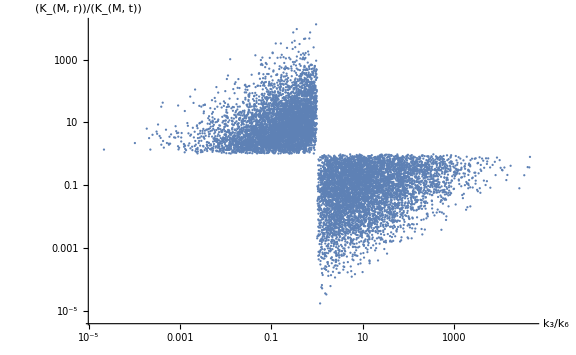

```mathematica
kdPlot=ListLogLogPlot[Transpose[{c1,c2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"k_3/k_6","(K_(M, r))/(K_(M, t))"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Minimal"]
```

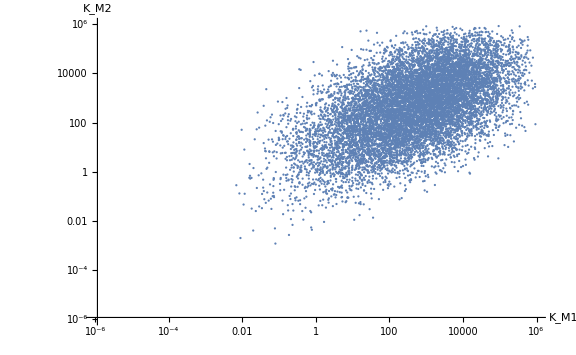

```mathematica
kmPlot=ListLogLogPlot[Transpose[{km1,km2}],ImageSize->Large,PlotRange->{{1.*10^-6,1.*10^6},{1.*10^-6,1.*10^6}},PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_M1","K_M2"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Default"]
```

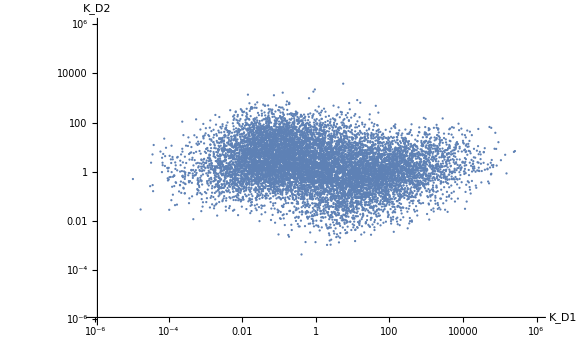

```mathematica
kdPlot=ListLogLogPlot[Transpose[{kd1,kd2}],ImageSize->Large,PlotRange->{{1.*10^-6,1.*10^6},{1.*10^-6,1.*10^6}},PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_D1","K_D2"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Default"]
```

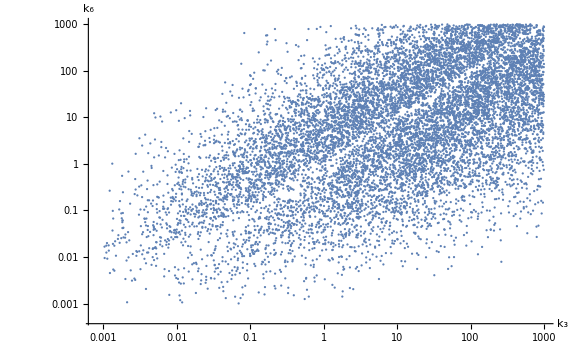

```mathematica
kdPlot=ListLogLogPlot[Transpose[{tKs[[3]],tKs[[6]]}],ImageSize->Large,PlotRange->PlotRange->{{1.*10^-3,1.*10^3},{1.*10^-3,1.*10^3}},PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"k_3","k_6"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Default"]
```

```mathematica
model=LinearModelFit[Transpose[{Log10[kd1],Log10[kd2]}],x,x]
```

FittedModel[0.269988-0.0961385 x]

```mathematica
InputForm[model["BestFit"]]
```

0.2699875341865057 - 0.09613846096912403*x

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.269988 | 0.00854528 | 31.5949 | 5.04797×10^-210
x | -0.0961385 | 0.00508217 | -18.9168 | 1.35135×10^-78

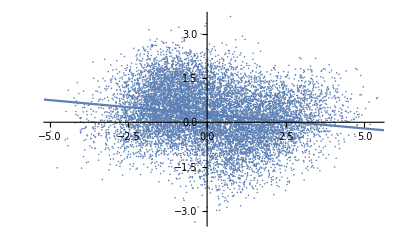

```mathematica
Show[ListPlot[Transpose[{Log10[kd1],Log10[kd2]}]],Plot[model["BestFit"],{x,-6,6}]]
```

```mathematica
ListPointPlot3D[DimensionReduce[Transpose[{km1,km2,kd1,kd2,tKs[[7]]}],3]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[DimensionReduce[bistableKs,3,Method->"PrincipalComponentsAnalysis",PerformanceGoal->"Quality"]]
```

-Graphics3D-

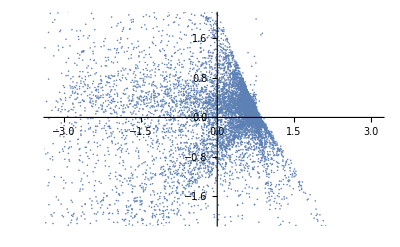

```mathematica
ListPlot[DimensionReduce[bistableKs,2,Method->"PrincipalComponentsAnalysis",PerformanceGoal->"Quality"]]
```

Conclusion:

These above results show that the parameter set within biological meaningful ranges can be reached by increasing the sampling size even when enforcing the thermodynamic constraint. Comparing to results from the other document (without enforcing thermodynamic constraint), the paramter space is largely reduced. 

Conditions | with thermo | with thermo | without thermo | without thermo
Sampling size | only check 
bistability | bistability &
 concentrations | only check 
bistability | bistability & 
concentrations
10^4 | 396 | N/A | 1448 | N/A
10^5 | 4378 | N/A | 14325 | N/A

#### From the sampling results, thermodynamic constraint indeed shrinks the parameter space for bistability in the motif. Although, the concentration is probably not very well sampled, the concentration is trivial for its purpose here.

Test analysis on parameters

## Test the code:

```mathematica
ndist = NormalDistribution[0,1];theta = Pi/8;
bigstd = 4.0; smallstd = 0.25;
alpha = N[Cos[theta]]; beta = N[Sin[theta]];
rv := 
{bigstd x1 alpha + smallstd y1 beta, bigstd x1 beta -
smallstd y1 alpha} /.
	{x1-> Random[ndist],y1-> Random[ndist]};

gprincipalaxes = Plot[{x (beta/alpha),
	x (-1/(beta/alpha))}, {x,-4,4},
	PlotRange->{{-4,4},{-4,4}},
	PlotStyle->{RGBColor[1,0,0]},
	AspectRatio->1,DisplayFunction->Identity];
```

```mathematica
npoints = 10;
rvsamples = Table[rv,{n,1,npoints}]
```

{{1.05129,0.568948},{-1.07512,-0.361079},{-5.98917,-3.08124},{0.66887,0.30387},{-3.7218,-1.63307},{-0.62023,0.0188301},{-3.49212,-1.69054},{0.0321029,0.233959},{0.580397,0.500489},{-5.80006,-2.40252}}

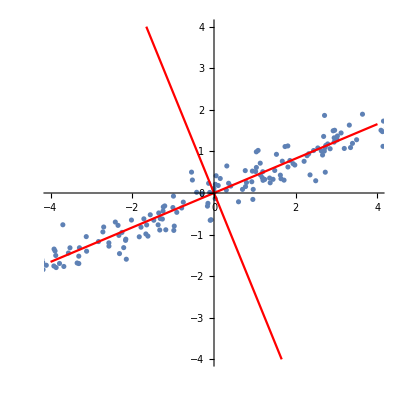

```mathematica
Show[g1,gprincipalaxes,
	DisplayFunction-> $DisplayFunction]
```

```mathematica
autolist = Table[
	Outer[Times,rvsamples[[i]],rvsamples[[i]]],
		{i,Length[rvsamples]}];
MatrixForm[auto=
	Sum[autolist[[i]],
		{i,Length[autolist]}]/Length[autolist]]
Clear[autolist];
```

(14.3588 | 5.87554
5.87554 | 2.48492)

```mathematica
auto
```

{{14.3588,5.87554},{5.87554,2.48492}}

```mathematica
MatrixForm[eigauto = Eigenvectors[auto]]
```

(-0.924871 | -0.380281
0.380281 | -0.924871)

```mathematica
gPCA = Plot[{eigauto[[1,2]]/eigauto[[1,1]] x,
	eigauto[[2,2]]/eigauto[[2,1]] x},
		{x,-4,4}, AspectRatio->1,
		DisplayFunction->Identity,
		PlotStyle->{RGBColor[1,.5,0]}];
```

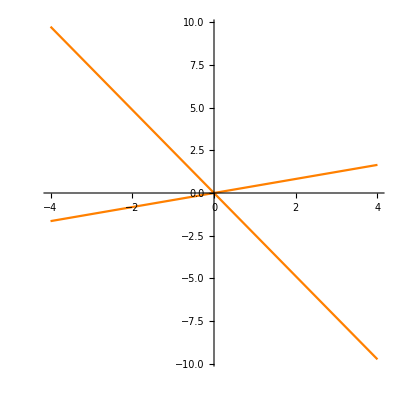

```mathematica
gPCA
```

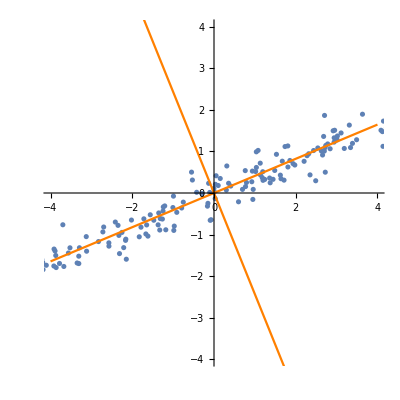

```mathematica
Show[g1,gPCA,DisplayFunction->$DisplayFunction]
```

```mathematica
g1 = ListPlot[rvsamples,PlotRange->{{-4,4},{-4,4}},
	AspectRatio->1, DisplayFunction->Identity];
```

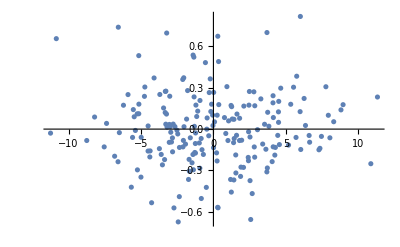

```mathematica
ListPlot[PrincipalComponents[rvsamples],PlotRange->Full]
```

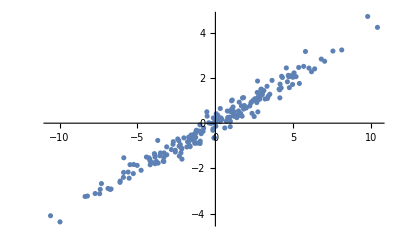

```mathematica
ListPlot[rvsamples,PlotRange->Full]
```

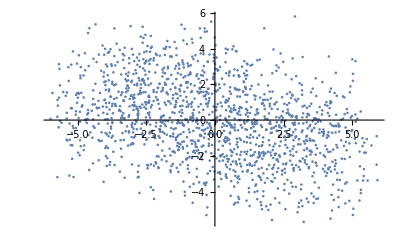

```mathematica
ListPlot[Transpose[Log10[{kd1,kd2}]],PlotRange->Full]
```

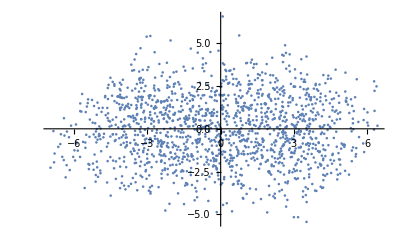

```mathematica
ListPlot[PrincipalComponents[Transpose[Log10[{kd1,kd2}]]]]
```

```mathematica
PrincipalComponents[Transpose[{kd1,kd2}]]
```

{{7864.65,2506.66},{7863.51,2611.62},{7849.33,2615.35},{7863.48,2614.22},{-73550.4,1711.53},{7863.72,2592.69},{7856.53,2615.16},{7865.6,2423.02},{7848.48,2615.32},{7864.01,2562.01},{7863.3,2589.46},{7600.32,2610.87},{7843.61,2615.13},{7877.05,1391.82},{7863.54,2007.04},{7863.34,2615.43},{7907.71,-1369.39},{-4198.57,2481.55},{7850.64,2559.79},{7858.53,2608.8},{7863.44,2615.49},{7865.27,2452.75},{7862.73,2567.94},{7863.04,2615.5},{7864.99,2432.01},{7863.49,2610.06},{7863.77,2588.12},{-228897.,-13.3608},{7862.99,2609.71},{7865.13,2466.16},{7863.78,2561.07},{7860.69,2615.},{7863.39,2609.89},{-16779.1,2341.68},{-8818.62,2372.67},{7864.12,2553.5},{7744.91,2613.99},{7863.52,2610.98},{7863.5,2612.94},{6958.01,2605.45},{7862.82,2615.49},{7867.41,2260.5},{7914.21,-1954.34},{7859.51,2614.95},{7858.73,2339.19},{-6140.19,-1153.81},{7843.58,2615.26},{7863.46,2614.15},{8032.36,-12690.},{-5683.35,2465.09},{7789.22,2614.39},{7863.46,2614.59},{7930.44,-3416.05},{3075.88,2562.34},{7859.92,2615.26},{7852.1,2410.57},{7863.16,2600.75},{7863.18,2615.37},{7061.03,2606.04},{7863.27,2615.47},{7863.62,2602.16},{-20546.4,2300.06},{7824.38,2615.07},{-13458.7,2378.3},{7836.66,2614.08},{7863.44,2615.19},{-101851.,1397.31},{7848.2,2612.75},{8425.1,-47966.9},{7803.49,2614.83},{4942.47,2582.54},{7220.01,2608.22},{7863.48,2614.2},{7859.54,2615.07},{-12503.3,2389.34},{8156.72,-23796.9},{7863.56,2607.56},{7863.44,2615.16},{7863.31,2615.25},{7857.24,2615.42},{7864.79,2495.13},{7767.65,2613.8},{-258265.,-339.41},{7878.31,1278.54},{7863.4,2615.44},{7859.92,2615.28},{7863.47,2615.39},{7969.84,-6964.49},{7969.49,-6933.99},{7858.87,2615.07},{7861.56,2615.47},{7856.38,2615.42},{7811.59,2614.52},{7863.47,2615.42},{7696.29,2047.39},{7864.49,2522.09},{7867.35,2260.76},{7863.62,2601.52},{7154.7,2607.42},{7863.51,2611.82},{7613.76,2612.57},{7847.59,2615.33},{7863.47,2615.32},{7863.88,2578.38},{7877.59,1252.01},{9400.23,-135789.},{5196.32,2583.97},{7874.2,1646.92},{7863.33,2613.65},{7863.32,2615.45},{-19432.3,2289.81},{7861.24,2614.97},{7860.62,2614.72},{7863.83,2582.7},{-183124.,494.902},{-25630.5,2243.17},{7863.36,2615.2},{7863.47,2615.5},{7853.94,2471.53},{7683.63,2612.75},{7863.39,2614.43},{7864.65,2508.45},{4876.23,2582.27},{7863.46,2615.28},{7863.47,2615.48},{7863.53,2610.52},{-766863.,-5986.68},{7862.39,2614.2},{7863.47,2615.5},{7770.91,2614.4},{7666.18,2613.31},{7865.6,2421.68},{7854.68,2614.89},{7851.44,2614.42},{7854.13,2305.63},{7863.47,2615.31},{6575.12,2601.15},{7863.47,2615.5},{7864.77,2489.09},{6505.64,2600.43},{7857.12,2594.43},{7863.47,2615.43},{7887.13,484.752},{7864.15,2553.92},{7863.66,2598.49},{4649.16,2571.56},{7863.47,2615.31},{-5592.04,2466.09},{7863.47,2615.49},{7863.47,2615.43},{7614.41,2612.67},{7850.51,2615.05},{7863.58,2605.53},{7847.27,2614.34},{7872.07,1839.54},{7854.59,2615.33},{7863.35,2614.31},{7015.88,2605.99},{7812.89,2614.91},{7863.27,2614.67},{7862.86,2614.92},{8018.48,-11345.6},{7872.83,1771.41},{7864.94,2482.91},{7936.74,-3983.51},{7863.51,2611.23},{-2380.82,2501.75},{7864.02,2563.81},{7676.31,2613.42},{7139.55,2607.39},{7706.93,2613.72},{7565.25,2609.14},{4247.49,2574.49},{7862.92,2615.5},{7855.51,2615.32},{7765.63,2614.38},{7843.41,2615.27},{7863.47,2615.5},{7863.57,2604.45},{7860.42,2599.72},{7696.54,2613.19},{7862.79,2615.04},{7863.47,2615.15},{7862.46,2614.9},{7869.83,2042.42},{7878.39,1272.11},{7874.54,1618.08},{7863.47,2615.5},{7862.55,2615.49},{7858.53,2615.45},{7863.53,2609.66},{7826.42,2615.08},{5228.04,2586.24},{7860.51,2615.39},{7861.91,2615.48},{7864.96,2481.69},{-73398.,1677.22},{7863.15,2615.37},{6405.51,2506.33},{7869.58,2032.97},{7863.47,2615.5},{7863.,2606.37},{7873.14,1737.93},{7864.09,2550.29},{7863.48,2614.28},{-194936.,360.732},{7863.47,2615.5},{7864.23,2530.5},{7863.9,2575.53},{7837.8,2615.21},{7858.13,2614.88},{7878.81,1233.74},{4299.88,2575.86},{8059.9,-15084.2},{7863.61,2602.52},{-2642.32,2498.82},{7863.48,2614.54},{7863.5,2612.95},{7862.62,2615.34},{7863.98,2568.42},{7863.03,2598.61},{-23337.3,2268.45},{7863.47,2614.95},{7859.96,2586.1},{7863.79,2573.63},{7864.47,2513.7},{7863.75,2590.14},{7863.51,2608.37},{7863.48,2609.46},{7863.47,2614.78},{7844.64,2562.16},{7863.68,2596.45},{7863.41,2615.5},{7867.7,2234.59},{7862.34,2516.88},{7863.46,2615.5},{7870.81,1953.5},{7299.37,2609.23},{7879.84,1132.34},{7933.72,-4263.88},{7863.28,2615.44},{7863.14,2516.43},{7882.94,811.624},{7466.2,2611.09},{-10742.4,2408.72},{7863.49,2613.59},{7842.53,2614.92},{7805.03,2614.84},{7863.47,2615.47},{6743.04,2603.06},{7874.12,1656.19},{7796.15,2613.56},{2996.31,2560.32},{7863.47,2615.46},{7863.9,2576.82},{7863.76,2587.97},{7865.29,2451.64},{7863.66,2598.14},{7715.3,2606.29},{7864.01,2566.42},{9355.,-131754.},{7864.86,2481.3},{5986.17,2594.65},{7863.83,2582.62},{7867.64,2240.21},{7865.95,2083.63},{7848.96,2615.29},{7855.68,2040.59},{7863.48,2614.81},{7839.88,2615.24},{7863.6,2603.75},{7862.98,2615.5},{7830.16,2611.69},{7863.52,2610.7},{7863.47,2615.31},{9314.52,-133727.},{3183.8,2563.54},{-7201.9,2443.58},{2914.71,2560.56},{-2012.8,2505.84},{4856.31,2582.1},{7862.3,2614.69},{7910.29,-1604.61},{7856.65,2615.43},{7924.44,-2876.02},{7525.47,2611.28},{7863.58,2604.08},{7863.38,2615.5},{7863.47,2615.09},{7821.73,2615.03},{7863.44,2615.33},{8836.74,-85079.},{-89764.8,1529.82},{7863.45,2614.76},{7863.97,2406.5},{7864.16,2552.5},{7863.47,2615.5},{5660.56,2590.3},{7819.49,2615.},{7855.78,2615.41},{3676.6,2567.85},{7807.6,2614.82},{7862.63,2609.78},{-27414.6,2223.8},{7863.56,2603.78},{7489.4,2611.27},{7868.69,2030.36},{7932.88,-3635.9},{7864.69,2505.01},{7863.6,2595.94},{7910.83,-1667.19},{7863.47,2615.34},{7862.76,2615.23},{7863.48,2613.67},{7848.43,2611.73},{7815.29,2614.97},{7865.51,2198.89},{7863.53,2608.38},{7863.45,2615.38},{7866.56,2329.48},{7860.43,2575.5},{7864.84,2483.67},{7863.58,2605.75},{7868.68,2146.07},{7863.46,2615.4},{7863.45,2611.83},{-24519.4,2255.48},{7718.79,2613.89},{7846.11,2615.31},{7863.35,2615.49},{7505.07,2611.29},{7863.24,2614.52},{7863.48,2614.9},{7855.25,2609.95},{7851.37,2546.26},{7688.71,2603.45},{7863.47,2615.05},{7864.66,2508.52},{7854.46,2615.4},{-54586.5,1922.1},{7863.47,2615.43},{7863.24,2614.89},{7863.47,2615.06},{6373.91,2572.92},{7863.47,2615.32},{7859.65,2615.46},{7439.08,2603.76},{7826.23,2612.66},{5555.23,2589.81},{7863.5,2612.85},{7779.06,2601.13},{7758.24,2614.32},{7860.78,2615.47},{7853.4,2483.05},{7844.65,2612.82},{7863.46,2615.04},{7866.48,2344.35},{7864.67,2507.13},{7871.57,1885.97},{7863.49,2613.33},{7866.93,2304.03},{7863.34,2613.1},{7863.45,2615.35},{-145001.,918.202},{7879.88,1133.22},{7863.56,2607.37},{7274.57,2591.74},{-8076.78,2427.11},{7858.15,2615.18},{7863.47,2615.28},{7863.47,2615.48},{7863.33,2614.06},{7862.28,2614.05},{7834.57,2614.4},{-50858.9,1963.43},{7638.47,2612.97},{-14765.3,2331.79},{7856.8,2615.37},{7866.52,2307.27},{7863.59,2603.79},{7805.5,2614.86},{7863.47,2615.5},{7676.5,-2733.65},{7244.49,2416.13},{7863.83,2583.49},{7863.55,2607.97},{7863.47,2615.46},{7817.18,2614.99},{7856.43,2206.99},{7863.77,2584.83},{7859.91,2614.92},{7863.64,2600.17},{7866.8,2315.89},{6552.28,2600.94},{7859.01,2615.45},{7886.92,503.35},{7863.84,2580.68},{7858.4,2562.92},{7863.48,2614.28},{7865.61,2422.83},{7864.96,2179.83},{5428.05,2586.27},{7892.41,8.73861},{7868.04,2203.85},{7863.4,2615.47},{7864.47,2525.28},{7833.31,2593.38},{7863.74,2586.94},{7863.42,2615.45},{5708.49,2591.46},{-2425.52,2494.23},{7854.4,2615.39},{7334.75,2607.7},{6935.03,2605.18},{7864.52,2519.13},{7896.36,-429.436},{7861.95,2606.04},{7863.43,2615.4},{7863.47,2615.5},{7863.47,2615.17},{7863.28,2609.86},{7863.4,2615.48},{7842.69,2610.02},{7863.31,2615.5},{8689.79,-71805.},{7863.85,2581.14},{7863.47,2615.44},{7863.57,2605.83},{7863.46,2615.32},{7863.11,2615.49},{7864.05,2563.49},{-23442.6,2267.9},{7500.33,2610.55},{7859.75,2291.6},{7895.33,-253.65},{7765.65,2575.42},{7863.96,2570.85},{7739.51,2614.13},{7729.87,2614.02},{7860.15,2614.78},{7863.47,2615.49},{-9764.54,2419.77},{6048.49,2588.93},{7877.73,1330.8},{7858.57,2610.86},{6650.44,2486.48},{7683.98,2613.27},{-1251.62,2514.28},{2943.48,2538.78},{7863.48,2614.26},{7863.48,2614.27},{7740.71,2614.14},{7862.77,2615.31},{7863.61,2598.99},{7862.01,2615.48},{7828.55,2611.05},{2612.14,2554.47},{7863.47,2615.42},{-11039.6,2405.61},{7862.31,2615.48},{7863.28,2615.49},{7863.51,2611.19},{7863.47,2614.96},{7863.3,2615.48},{7863.41,2576.58},{7860.98,2614.35},{-97631.9,1286.51},{7881.96,944.438},{7863.47,2615.45},{7863.47,2615.15},{7865.68,2414.89},{7863.56,2606.01},{49.3576,2528.53},{5502.92,2587.14},{9256.28,-122832.},{-16340.7,2346.75},{7859.35,2615.44},{7691.35,2612.14},{7863.3,2615.5},{7828.37,2615.11},{-57749.4,1886.76},{7789.82,2614.39},{7781.96,2614.6},{7712.,2613.82},{7863.46,2615.5},{9354.35,-131658.},{-6851.12,2450.41},{7848.62,2614.5},{8300.81,-36773.3},{7863.22,2615.48},{7859.56,2615.46},{7863.47,2615.37},{-15408.6,2357.1},{7788.73,2614.39},{7861.2,2605.68},{7863.47,2615.5},{7978.19,-7719.97},{7863.31,2615.43},{6786.8,2588.22},{7727.68,2613.96},{7764.13,2608.54},{7778.45,2614.54},{7863.95,2572.2},{7858.7,2615.45},{7863.46,2613.01},{7875.11,1567.43},{7862.64,2615.49},{7865.5,2353.68},{7325.26,2573.5},{-313.458,2389.88},{3726.13,2569.2},{7863.46,2614.91},{7911.25,-1688.76},{7863.47,2615.48},{5085.94,2584.22},{7865.77,2407.7},{7863.54,2608.59},{7861.53,2614.84},{7806.17,2614.87},{7850.19,2613.33},{7851.29,2614.72},{7863.48,2614.39},{7863.42,2607.37},{-3586.93,2478.26},{7957.37,-5841.7},{7138.05,2607.45},{7865.96,2391.22},{7688.9,2613.56},{7860.62,2615.47},{7887.21,477.233},{-77394.3,1592.18},{7901.7,-830.46},{7863.25,2615.5},{7863.48,2614.1},{7863.64,2600.32},{-817393.,-6547.6},{-8338.5,2435.61},{7793.69,2614.72},{7863.44,2609.94},{-7964.25,2431.15},{7873.6,1703.25},{7863.37,2615.47},{7863.49,2610.24},{7863.47,2615.42},{7855.05,2615.4},{7863.45,2615.48},{7863.49,2613.58},{7863.04,2615.32},{7862.17,2615.49},{7863.84,2582.2},{7865.95,1930.76},{7863.46,2615.5},{7863.45,2615.5},{7863.82,2582.41},{7863.48,2614.14},{7875.28,1548.2},{7863.45,2615.5},{7863.47,2615.34},{7861.1,2615.38},{7187.51,2584.6},{7859.98,2615.42},{7866.88,2308.41},{7358.14,2609.89},{7862.99,2603.66},{7880.19,1109.69},{7870.24,2006.06},{7860.6,2615.37},{7863.46,2615.5},{7863.42,2614.77},{7863.76,2589.33},{7956.98,-6072.71},{7863.41,2614.89},{7874.79,1559.81},{7863.72,2593.31},{7859.68,2611.1},{7854.47,1376.21},{7338.89,2609.36},{6293.35,2598.06},{7862.87,2615.46},{7862.94,2615.5},{-10231.9,2414.08},{-328843.,-1123.15},{7863.86,2580.37},{7863.14,2615.49},{7855.05,2613.49},{1926.58,2548.47},{7922.32,-2912.32},{7859.43,2615.01},{7842.72,2534.16},{7940.05,-4281.23},{7865.25,2454.71},{7863.2,2615.5},{7872.52,1662.32},{7851.27,2615.36},{7855.69,2615.42},{7188.1,2607.98},{7863.47,2615.2},{7863.4,2615.01},{-59306.4,1867.17},{7863.47,2615.5},{7863.47,2615.46},{-250959.,-258.295},{7769.46,2614.46},{7863.54,2608.71},{7863.47,2615.49},{7867.51,2240.45},{7863.47,2615.47},{7939.16,-4725.81},{-38436.2,2100.22},{7863.51,2611.76},{-98131.8,1057.52},{7851.89,2615.31},{7754.57,2597.97},{7863.48,2614.47},{7847.89,2615.33},{7858.44,2615.42},{7863.46,2615.5},{6847.98,2604.23},{7823.52,2615.04},{-23825.8,2263.65},{-31511.7,2177.26},{7863.43,2615.39},{7863.49,2613.1},{7836.56,2591.09},{7863.57,2606.21},{7863.47,2615.5},{7863.5,2612.39},{7812.57,2606.79},{7860.93,2615.47},{7866.73,2235.29},{7861.86,2615.48},{7744.97,2199.57},{7855.83,2610.97},{7855.5,2594.87},{7861.33,2615.23},{7863.66,2307.01},{7872.46,1805.59},{-1037.34,2516.38},{-5807.,2463.59},{5655.09,2589.5},{7868.62,2150.8},{7868.62,2151.92},{3538.7,2567.48},{7863.54,2607.18},{7863.39,2615.5},{7826.28,2517.17},{7863.47,2615.47},{7863.46,2615.2},{13994.7,-623313.},{7863.43,2615.45},{7861.97,2614.46},{3798.05,2569.08},{7374.1,2609.92},{7863.57,2606.63},{7863.48,2614.35},{7801.2,2608.32},{5975.27,2594.49},{7861.75,2609.63},{7840.73,2615.24},{7885.26,631.719},{5636.54,2585.95},{7863.44,2615.49},{6732.06,2602.3},{7863.47,2612.79},{7127.17,2607.33},{7863.47,2615.43},{7644.25,2613.06},{7903.98,-1034.81},{7853.65,2615.02},{7863.46,2615.26},{7849.79,2611.21},{7863.47,2615.17},{7639.79,2613.02},{7748.45,2613.89},{7914.77,-2062.35},{6645.49,2601.97},{7494.86,2611.41},{7859.74,2615.44},{7731.86,2614.03},{7863.49,2613.97},{-196302.,348.584},{7862.69,2612.65},{7526.5,2611.76},{7860.99,2605.62},{7970.59,-7031.92},{7891.69,73.3532},{7863.48,2614.82},{7867.61,2231.28},{7863.48,2614.61},{7848.41,2615.33},{7857.73,2615.43},{5973.96,2594.52},{7863.48,2614.25},{7862.6,2614.47},{7863.44,2615.5},{7876.29,1448.93},{7863.48,2614.69},{9700.3,-162815.},{7910.41,-1611.7},{7863.43,2614.83},{7916.7,-2213.07},{7877.29,1370.74},{7887.63,438.781},{7866.5,2341.87},{7863.47,2615.11},{5050.37,2584.25},{7863.73,2592.12},{7863.49,2604.94},{7863.87,2579.02},{7863.37,2615.39},{7905.56,-1175.14},{7863.48,2614.53},{7316.13,2609.41},{6161.81,2596.61},{7863.49,2613.66},{7700.96,1465.45},{7755.85,2614.12},{7877.37,1363.85},{7403.02,2607.73},{7863.46,2615.04},{7630.1,2612.9},{7789.63,2614.68},{7863.21,2615.49},{7810.21,2614.91},{7863.46,2615.48},{7974.47,-7382.45},{7863.28,2593.52},{8007.14,-10752.7},{7810.77,2614.88},{7863.47,2615.46},{7858.24,2614.23},{-17651.1,2331.73},{7887.89,410.096},{7862.97,2615.5},{7387.09,2610.09},{7863.58,2605.48},{7640.02,2611.66},{7848.57,2589.52},{7805.28,2614.86},{7857.15,2615.43},{7822.05,2614.9},{7864.16,2553.24},{-7276.13,2447.4},{7851.55,2545.05},{7311.58,2609.37},{-33666.8,2154.37},{3148.21,2563.11},{7893.35,-75.9567},{7833.6,2613.21},{7863.49,2613.71},{7863.44,2615.38},{7862.78,2576.38},{7797.26,2614.77},{7863.47,2615.5},{-10319.1,2413.62},{7863.56,2579.08},{-846.086,2518.67},{7867.1,2288.9},{7870.35,1995.77},{3179.76,2346.04},{-265227.,-416.725},{7863.45,2612.68},{7866.96,2220.14},{7866.07,2374.69},{7568.95,2610.87},{7863.49,2613.23},{7859.48,2612.63},{7863.02,2615.2},{6343.19,-758.628},{7857.94,2615.44},{7863.25,2615.48},{7864.46,2526.07},{7874.03,608.491},{-54220.6,1926.14},{7863.5,2613.05},{5678.52,2591.24},{7576.65,810.382},{7863.51,2577.69},{-13427.3,2379.1},{7862.58,2615.48},{6378.95,2553.03},{5710.37,2591.59},{7866.99,2288.26},{-12149.,2393.3},{7863.36,2579.5},{7806.36,2614.76},{7863.46,2615.37},{7863.62,2599.27},{7863.53,2609.83},{7863.42,2615.47},{7863.44,2615.5},{6309.18,2592.52},{-24233.8,2259.12},{6468.22,2600.01},{7863.13,2615.49},{7822.78,2615.04},{-1427.13,2512.13},{7863.47,2614.79},{7863.83,2582.78},{7902.45,-908.875},{7863.26,2614.29},{-762567.,-5938.85},{7830.62,2614.27},{7863.5,2612.59},{7860.32,2609.66},{7891.9,39.8647},{8027.25,-12135.2},{7867.2,2276.8},{7808.,2605.93},{7863.47,2615.5},{7863.54,2605.55},{7863.46,2615.19},{7863.01,2585.91},{7795.76,2601.08},{7859.1,2615.44},{7869.96,2030.84},{7863.51,2612.2},{7811.65,2614.93},{7858.83,2554.37},{7863.26,2614.69},{-91801.7,1508.61},{-493005.,-2945.84},{7864.,2567.08},{7864.56,2517.07},{7863.23,2615.49},{7970.71,-7265.21},{7927.59,-3159.54},{7839.13,2615.12},{7863.52,2610.59},{7757.36,2614.33},{7153.07,2607.61},{1616.88,2545.95},{7863.38,2615.5},{7832.06,2615.11},{-37842.1,2086.77},{9853.,-176567.},{7874.74,1590.47},{7812.94,2614.94},{-18560.9,2322.06},{7863.47,2615.49},{7844.88,2615.29},{7863.47,2615.27},{7850.91,2589.32},{7861.65,2615.3},{7863.54,2609.02},{7863.48,2614.21},{7860.49,2615.47},{7863.54,2609.37},{7826.61,2612.62},{7130.35,2607.33},{7863.15,2614.47},{7599.93,2612.21},{7863.4,2614.98},{7838.,2614.79},{7860.79,2615.46},{7863.39,2615.5},{7853.23,2576.41},{7863.75,2590.58},{7863.6,2603.49},{6342.04,2597.21},{8098.72,-18571.7},{7115.72,2606.67},{7746.22,2609.94},{7778.58,2527.66},{-276.159,2521.63},{7868.04,2202.37},{7865.12,1160.67},{-301464.,-819.078},{7864.38,2528.05},{7863.67,2597.06},{4295.94,2575.89},{7863.4,2615.5},{7863.43,2612.99},{5322.48,2585.21},{7863.13,2611.79},{7841.25,2614.47},{7863.49,2613.98},{7864.79,2496.22},{7862.84,2614.85},{7861.68,2594.86},{7852.06,2614.61},{7863.43,2613.83},{6951.59,2605.26},{7863.22,2615.43},{7863.47,2615.32},{7863.35,2615.29},{7863.47,2615.5},{7857.56,2615.43},{7845.18,2615.2},{-8743.59,2420.68},{7885.35,644.376},{7735.72,2614.06},{7861.05,2602.18},{7863.47,2615.14},{7863.,2615.48},{7863.7,2595.15},{7914.65,-1994.29},{7864.19,2547.37},{7600.84,2611.83},{7863.4,2614.38},{7863.42,2615.5},{7865.22,2457.63},{7863.48,2614.7},{2813.15,2559.43},{7862.3,2615.32},{7863.44,2614.53},{3238.83,2562.9},{7864.51,2522.02},{7862.87,2613.48},{7859.98,2615.46},{7863.12,2614.97},{7807.53,2601.57},{-144347.,924.252},{8307.29,-37383.9},{7863.47,2615.37},{7863.47,2615.4},{7863.09,2607.34},{2224.3,2552.89},{7863.51,2611.83},{7863.45,2615.5},{7864.81,2416.42},{7841.53,2615.26},{7863.56,2583.9},{7827.23,-6309.39},{-43713.3,2024.43},{7864.41,2530.9},{-8895.98,2429.42},{9354.29,-131678.},{4573.54,2578.74},{7863.55,2608.08},{7918.99,-2384.47},{7897.23,-528.728},{7863.44,2607.86},{3206.03,2563.78},{7865.92,2394.58},{7523.65,2611.73},{7863.47,2615.5},{7857.86,2615.44},{4431.96,2577.12},{7863.09,2615.46},{3835.24,2570.78},{7863.48,2613.97},{7671.88,2609.25},{7815.92,2614.47},{7833.47,2615.17},{-45054.3,2025.77},{7638.83,2612.6},{7863.48,2614.8},{7882.88,867.072},{7859.,2340.21},{-14324.2,2368.68},{7488.87,2262.76},{7865.18,2461.06},{7863.5,2613.01},{7861.08,2614.21},{7863.88,2578.02},{7862.3,2607.71},{7858.69,2611.75},{7835.94,2615.19},{7243.25,2607.13},{6242.19,2595.11},{7863.55,2607.35},{7863.84,2582.07},{36.3547,2526.54},{7863.54,2609.48},{7763.77,2606.33},{7864.4,2532.03},{11424.1,-318132.},{7941.26,-4390.77},{7863.07,2615.4},{7884.11,674.681},{7863.18,2615.35},{7682.27,2613.23},{7856.91,2612.94},{7860.23,2615.46},{-4641.24,2470.31},{7876.92,1399.85},{7831.84,2615.15},{7920.4,-2512.24},{-239467.,-130.694},{7863.43,2605.42},{1393.33,2543.36},{7708.58,2613.77},{-47310.7,2002.89},{7863.26,2615.13},{7914.19,-2034.29},{7512.99,2611.5},{7860.95,2611.91},{7860.18,2615.39},{-49296.6,1980.45},{7862.4,2611.95},{7782.66,2613.47},{7863.87,2578.75},{7846.21,2615.31},{7863.46,2615.46},{7860.96,2615.47},{-226032.,18.3822},{7849.3,2615.33},{7865.,2477.33},{7863.37,2614.74},{6960.08,2320.19},{7863.01,2615.5},{7841.05,2615.25},{7855.85,2612.33},{7861.11,2615.42},{7425.39,2610.64},{7863.47,2615.5},{7863.5,2613.09},{7863.48,2614.38},{-5393.7,2468.3},{7863.44,2615.5},{7863.48,2614.41},{7863.64,2599.77},{7863.47,2615.38},{7864.61,1633.69},{7863.01,2607.18},{7865.67,2417.31},{7734.59,2614.07},{7662.73,2613.27},{-70768.6,1742.38},{7863.43,2615.47},{7862.97,2615.5},{7863.47,2614.7},{4229.51,2517.83},{7853.27,2615.39},{7852.97,412.608},{7863.61,2602.66},{7859.46,2615.45},{-5698.05,2464.72},{6092.49,2595.82},{7743.35,2614.17},{7848.77,2615.23},{7871.84,1858.3},{7775.83,2614.53},{8179.76,-25876.9},{7859.9,2612.35},{7863.47,2615.3},{7863.88,2553.93},{7664.37,1744.87},{7528.58,2611.77},{7863.47,2615.17},{7863.48,2614.88},{7863.37,2527.65},{7863.46,2615.29},{7824.78,2615.07},{7866.77,2290.1},{8515.3,-56090.8},{7863.22,2615.43},{7863.47,2614.88},{8123.4,-20797.5},{7863.93,2574.19},{7862.89,2615.34},{7864.17,2551.74},{7859.77,2612.38},{7863.32,2615.49},{7863.47,2615.27},{7857.94,2615.44},{7863.42,2615.48},{-2295.66,2502.69},{7863.47,2615.5},{7863.42,2615.48},{7863.69,2501.04},{7879.44,1177.1},{5766.98,2592.15},{7856.02,1500.53},{7863.53,2559.86},{7873.54,1708.49},{7868.2,2151.88},{7863.48,2614.74},{10273.2,-214415.},{7661.76,2613.26},{7840.23,2614.63},{7706.96,2613.77},{7863.47,2615.07},{7863.51,2612.11},{6478.59,2600.13},{7833.77,2615.17},{7863.45,2615.49},{7861.64,2615.08},{7834.61,2600.92},{7217.81,2608.33},{-7360.47,2407.71},{7865.49,2410.92},{7863.48,2614.81},{-97128.,1449.75},{5485.35,2588.76},{7863.43,2609.72},{7863.47,2615.36},{7859.71,2615.46},{7863.21,2615.15},{7430.51,2610.67},{7863.25,2615.47},{7862.09,2615.49},{7913.28,-1870.51},{7857.27,2615.39},{7863.69,2595.14},{7889.43,277.045},{7864.5,2522.48},{8003.42,-9990.49},{7861.07,2615.42},{-126948.,1118.6},{7556.77,2612.09},{7863.54,2608.75},{7863.35,2614.01},{7863.35,2615.5},{7864.15,2553.25},{-125089.,1138.48},{7856.59,2615.4},{7860.03,2614.85},{-34859.,2141.14},{7862.93,2615.14},{7856.18,2565.51},{7863.25,2615.5},{7586.4,2612.43},{7864.38,2527.99},{7497.5,2611.},{7868.08,2196.65},{7856.89,2615.43},{-197457.,335.762},{7860.7,2615.47},{-117152.,1227.33},{7861.32,2615.41},{7853.11,2575.18},{7863.22,2585.45},{7881.2,1018.54},{7493.96,2611.36},{7863.37,2615.5},{7912.56,-1806.73},{5328.03,2587.35},{7863.48,2614.81},{7863.64,2600.17},{7863.86,2579.91},{7863.37,2615.5},{-15427.2,2356.9},{7863.41,2615.34},{-55541.7,1907.36},{7102.43,2606.43},{7864.55,2491.58},{7863.48,2614.35},{7862.73,2615.48},{7863.27,2615.46},{7863.61,2602.16},{6738.62,2603.01},{1046.41,2539.8},{7817.3,2285.61},{7818.84,2615.01},{7524.9,2603.61},{7856.27,2615.42},{7829.05,2615.02},{7856.85,2568.12},{7864.12,2556.68},{7863.46,2615.49},{7862.39,2610.19},{7868.62,2151.85},{7863.43,2615.43},{7861.73,2615.47},{7851.27,2615.36},{799.384,2536.22},{7863.55,2608.04},{7862.65,2553.15},{4827.86,2581.78},{7483.87,2611.29},{7861.93,2615.49},{7863.49,2613.58},{7863.14,2615.47},{7860.95,2615.47},{7357.34,2600.97},{7223.92,2606.66},{7641.71,2612.53},{7854.15,2610.64},{-18851.8,2318.42},{7863.68,2596.37},{7863.67,2597.58},{7863.47,2615.3},{7879.65,1157.83},{7921.97,-2680.01},{7828.18,2612.74},{7582.5,2611.39},{7798.22,2610.59},{8095.68,-18311.8},{7863.53,2610.14},{7863.55,2608.08},{7864.44,2527.92},{7863.54,2609.07},{7863.6,2577.29},{7507.37,2611.55},{7862.86,2615.45},{7863.48,2614.41},{8241.14,-31411.3},{7863.46,2615.49},{7698.43,2613.66},{7863.74,2579.05},{7863.87,2574.43},{6916.8,2603.73},{7359.77,2607.83},{7863.52,2610.88},{-85656.8,1576.88},{7860.96,2615.36},{7863.68,2576.11},{7860.63,2603.64},{6986.38,2604.26},{10375.6,-223638.},{-26673.4,2231.57},{7863.47,2615.5},{7863.47,2615.46},{3899.6,2571.49},{7197.59,2608.11},{7863.47,2615.44},{7863.47,2615.25},{7863.41,2615.44},{7863.49,2613.16},{6116.64,2596.04},{7785.07,2614.63},{6606.65,2601.55},{7863.62,2601.65},{7863.47,2615.47},{-1368.22,2512.83},{7862.59,2615.36},{7857.24,2615.34},{7862.68,2615.45},{7863.47,2615.5},{-42056.9,2061.18},{7862.02,2615.42},{7802.38,2614.81},{7861.26,2615.47},{7863.72,2590.4},{7863.46,2615.5},{7868.54,2158.01},{7863.44,2615.49},{7863.13,2615.22},{7996.79,-9393.51},{8322.99,-38858.9},{7856.63,2615.43},{6210.99,2596.5},{7836.69,2614.97},{7871.81,1859.77},{7861.51,2615.48},{7982.82,-8134.02},{7855.89,2615.42},{7861.9,2613.74},{7865.61,2419.34},{7029.35,2592.2},{7854.94,2614.4},{7863.5,2612.41},{8072.52,-16212.1},{7848.86,2615.06},{7863.32,2614.2},{5650.15,2590.8},{7863.81,2585.03},{5081.17,2578.62},{7862.51,2615.49},{7863.08,2615.24},{7855.11,2615.41},{7863.45,2615.38},{7863.67,2597.7},{6403.82,2599.09},{7864.58,2515.87},{7862.75,2615.14},{7863.47,2615.37},{7501.34,2611.47},{7863.47,2615.46},{7217.95,2581.88},{7903.71,-1011.17},{7752.82,2614.26},{7863.43,2614.62},{6704.54,2602.55},{7190.72,2606.34},{7843.63,2615.23},{7883.8,734.89},{-122143.,1169.95},{7863.74,2590.99},{7837.29,2614.56},{7861.54,2615.45},{7118.11,2607.23},{7646.51,2612.97},{7864.65,2509.57},{7866.51,2322.55},{7761.33,2613.56},{2304.8,2552.99},{7863.48,2614.78},{7863.37,2615.5},{7863.48,2614.86},{7867.27,2272.59},{7863.47,2615.5},{7863.48,2614.76},{7898.49,-538.305},{7863.47,2615.06},{7862.04,2306.99},{7863.47,2615.03},{7863.53,2609.91},{3216.26,2563.29},{7862.95,2571.82},{7863.49,2613.76},{7862.87,2615.41},{4523.83,2578.41},{7860.18,2613.9},{7264.25,2608.85},{7585.6,2612.42},{7833.89,2614.94},{7875.47,1534.4},{7863.23,2612.81},{7863.47,2615.49},{7864.65,2508.45},{7864.35,2531.26},{7863.48,2614.09},{7960.21,-6486.3},{7863.49,2613.44},{7863.82,2576.98},{7863.54,2609.4},{7750.12,2614.24},{7863.4,2615.5},{7867.31,2249.15},{7868.5,2151.36},{7863.45,2615.15},{7863.47,2615.5},{7909.59,-1538.13},{7860.64,2546.95},{7870.02,1919.93},{7681.42,2613.48},{-17413.3,1894.12},{7863.46,2614.63},{7863.43,2614.84},{6910.85,2603.26},{7863.46,2615.5},{3928.02,2571.81},{7863.8,2585.65},{7862.6,1303.26},{7858.24,2615.06},{8379.83,-43889.2},{7863.69,2595.95},{7863.5,2612.22},{6340.7,2598.6},{1370.52,2538.02},{7863.49,2613.5},{7861.95,2615.49},{7863.47,2614.26},{7863.32,2615.49},{7861.77,2615.48},{5606.01,2590.41},{7863.47,2615.43},{7856.59,2613.3},{7863.06,2615.5},{7896.15,-327.929},{7855.86,2614.42},{7863.53,2609.81},{7863.31,2615.49},{7847.68,211.67},{4296.99,2575.9},{7068.42,2605.94},{7863.47,2615.42},{7456.84,2608.57},{7860.72,2615.41},{7863.47,2614.7},{7862.96,2614.76},{7863.46,2615.41},{7918.47,-2338.57},{7863.54,2603.03},{-70350.4,1747.07},{7510.29,2611.46},{-7970.5,2439.06},{7749.56,2613.9},{7865.33,2447.81},{7814.86,2614.96},{7863.47,2615.3},{7863.52,2611.26},{6795.86,2603.61},{7857.93,2611.76},{7800.28,2587.07},{7875.55,1517.38},{7863.67,2592.56},{7723.73,2613.57},{7863.48,2613.86},{7863.51,2611.3},{7869.09,2108.75},{7799.33,2613.21},{7863.47,2615.3},{7186.93,2607.33},{2623.51,2557.3},{7877.92,1307.44},{-751.034,2519.85},{7880.24,885.796},{7863.54,2608.84},{7863.47,2615.5},{-8206.28,2437.06},{-20743.5,2297.84},{7863.47,2615.48},{8004.4,-10077.8},{-17965.8,2326.73},{7863.37,2615.49},{7863.34,2611.8},{7876.19,1470.15},{7863.48,2614.87},{7863.35,2615.5},{7829.64,2614.49},{7863.35,2614.18},{7863.25,2607.75},{-174734.,588.063},{7851.49,2615.35},{7863.4,2614.99},{-4746.19,2475.35},{-3360.75,2490.88},{7813.87,2614.94},{7864.44,2528.24},{7863.47,2599.43},{-45091.,2027.52},{7849.31,2605.04},{6922.81,2593.75},{-25427.1,2245.64},{6977.09,2605.66},{-354332.,-1406.08},{7584.47,2593.43},{8873.02,-88353.4},{7514.07,2611.62},{7576.4,2612.31},{-31668.7,2176.49},{7864.45,2527.24},{7863.53,2610.25},{-48280.5,1992.12},{-34555.3,2144.51},{7863.31,2593.85},{7863.42,2615.36},{7863.6,2603.64},{7440.37,2581.85},{7844.93,2615.29},{7712.63,2605.82},{-4027.76,2483.37},{7863.52,2558.65},{-266301.,-428.693},{5665.49,2591.1},{4717.68,2580.56},{7863.86,2579.92},{7863.47,2615.4},{-20300.6,2302.79},{7863.98,2569.54},{7738.2,2575.33},{-9351.14,2414.66},{7770.98,2612.13},{4604.72,2579.32},{7822.86,2615.02},{7863.69,2595.24},{7858.43,2615.45},{4694.77,2544.21},{-79911.4,1639.53},{6712.28,2602.64},{7883.07,850.165},{7862.79,2615.49},{7863.4,2615.29},{1770.08,2547.85},{7863.47,2615.5},{7821.43,2615.04},{7872.08,1839.38},{7848.54,2615.33},{7865.31,2449.98},{7830.22,2615.13},{5233.87,2586.3},{7863.47,2615.5},{7009.23,2605.72},{3799.15,2570.31},{7863.47,2615.4},{-4288.69,2480.57},{7863.87,2579.07},{7857.74,2563.5},{7862.13,2615.47},{7835.25,2615.17},{7863.47,2615.43},{7863.57,2606.28},{6324.84,2598.16},{7828.59,2615.12},{7863.46,2615.44},{7847.53,2613.76},{7863.57,2606.32},{5620.38,2590.57},{-92487.4,-1012.59},{7863.47,2614.84},{7863.52,2610.35},{7863.54,2609.49},{7835.6,2615.19},{-176172.,572.072},{7863.52,2610.97},{7819.13,2596.79},{7986.14,-8432.83},{7834.98,2614.61},{7709.71,2613.78},{7860.79,2614.62},{7863.83,2582.67},{-17308.6,2336.01},{7220.14,-214.765},{5019.06,2583.83},{7863.48,2614.71},{7884.69,704.315},{7863.43,2614.77},{7937.77,-4076.54},{7863.53,2609.8},{7863.47,2609.24},{7863.46,2615.5},{-5090.33,2469.17},{7863.32,2614.63},{7870.61,1879.39},{7413.89,2606.63},{7845.15,2615.3},{7864.7,2496.52},{7863.47,2615.38},{7852.08,2293.82},{7863.43,2615.5},{7863.46,2615.49},{7758.06,2613.72},{7869.19,1981.65},{7865.09,2469.84},{7966.11,-6629.02},{7863.41,2615.46},{-123119.,-809.535},{6711.12,2602.71},{7863.7,2595.09}}

```mathematica
autolist = Table[
	Outer[Times,rvsamples[[i]],rvsamples[[i]]],
		{i,Length[rvsamples]}]
```

{{{1.10521,0.598128},{0.598128,0.323702}},{{1.15588,0.388203},{0.388203,0.130378}},{{35.8701,18.4541},{18.4541,9.49406}},{{0.447387,0.20325},{0.20325,0.0923371}},{{13.8518,6.07794},{6.07794,2.6669}},{{0.384686,-0.011679},{-0.011679,0.000354574}},{{12.1949,5.90356},{5.90356,2.85792}},{{0.0010306,0.00751079},{0.00751079,0.054737}},{{0.336861,0.290483},{0.290483,0.25049}},{{33.6406,13.9347},{13.9347,5.77209}}}

```mathematica
rvsamples
```

{{1.05129,0.568948},{-1.07512,-0.361079},{-5.98917,-3.08124},{0.66887,0.30387},{-3.7218,-1.63307},{-0.62023,0.0188301},{-3.49212,-1.69054},{0.0321029,0.233959},{0.580397,0.500489},{-5.80006,-2.40252}}

```mathematica
Outer[Times,rvsamples[[3]],rvsamples[[3]]]
```

{{35.8701,18.4541},{18.4541,9.49406}}

### test2

```mathematica
DimensionReduction[Transpose[{km1,km2,kd1,kd2,tKs[[7]]}],2]
```

DimensionReducerFunction[…]

```mathematica
ListPointPlot3D[DimensionReduce[Transpose[{km1,km2,kd1,kd2,tKs[[7]]}],3]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[DimensionReduce[bistableKs,3,Method->"PrincipalComponentsAnalysis",PerformanceGoal->"Quality"]]
```

-Graphics3D-

```mathematica
Eigenvectors[bistableKs,3]
```

Eigenvectors[{{118.318,0.00250532,54.4829,1.64527,8.32862,0.254646,7.05166,2.26688,78.0825,0.385848,0.0035448},{1},1509,{1},{42.1982,0.00140527,545.324,0.136494,3,0.0405895,245.802,0.109542,0.00536507}},3]
 |  |  |  |

```mathematica
others=Exp[RandomReal[{0,1},3]*2*Log[1000]-Log[1000]];
While[(rand1s=RandomReal[{0,1},4];sum=Total@rand1s;psum=Switch[True,0≤#≤1,1./4*sum^3,1<#≤2,1/4*(-3*sum^3+12*sum^2-12*sum+4),2<#≤3,1/4*(3*sum^3-24*sum^2+60*sum-44),3<#≤4,1/4*(-sum^3+12*sum^2-48*sum+64)]&[sum];
RandomReal≤psum)];
rand23=RandomVariate[DirichletDistribution[{1,1,1,1}]];
rand21=1-Total@rand23;
k1=Exp[rand1s[[1]]/sum*2*Log[1000]-Log[1000]];k2=Exp[rand23[[1]]*2*Log[1000]-Log[1000]];k3=others[[1]];k4=Exp[rand23[[2]]*2*Log[1000]-Log[1000]];k5=Exp[rand1s[[2]]/sum*2*Log[1000]-Log[1000]];k6=others[[2]];k7=others[[3]];
k8=Exp[rand23[[3]]*2*Log[1000]-Log[1000]];
k9=Exp[rand1s[[3]]/sum*2*Log[1000]-Log[1000]];
k10=Exp[rand1s[[4]]/sum*2*Log[1000]-Log[1000]];
k11=Exp[rand21*2*Log[1000]-Log[1000]];
{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11}
```

{0.00750792,0.00420812,0.190122,0.119364,0.0518549,0.0352926,0.859202,0.00173542,0.610612,0.00420654,1.14719}